# Shor’s Algorithm for Factorization

## Key Concepts

Hybrid algorithm

Shor’s algorithm

Order finding problem

## Integer Factorization and Hybrid Algorithms

In many applied areas (like cryptography, for example) algorithms to efficiently factor integers are important. For special classes of integers, such algorithms are known and used. It turns out that the problem of factoring integers can be mathematically reduced to a slightly different problem, for which an efficient quantum algorithm exists. Shor’s algorithm for order finding is the quantum part of a hybrid algorithm for factoring integers.

In a hybrid algorithm, the problem is first given some classical pre-processing to turn the original problem into one for which a quantum algorithm is known. Then, the output of the quantum algorithm can be given some classical post-processing to arrive at the answer to the original problem. Sometimes, this loop may even be repeated, depending on the problem to be solved. If the classical pre-processing and post-processing can be done efficiently, then the quantum partial solution can be used to solve the whole problem more efficiently than would be possible classically.

## Factorization Through Order Finding

Before presenting the quantum part of the algorithm, let’s first examine how the multiplicative order finding problem can be related to factoring integers.

Suppose that you want to factor the number 𝒩. If 𝒩 is even, or if 𝒩 is a prime power, it turns out that fast algorithms exist to determine these facts. Such numbers are also fast to factor. Therefore, assume that 𝒩 is neither even nor a prime power.

As an example, let’s take the number 𝒩 to be 15.

```mathematica
𝓃=15;
Comap[{EvenQ,PrimePowerQ},𝓃]
```

{False,False}

Consider what happens if you compute 𝒶^𝓇 mod 𝒩 for all the possible 𝒶 between 2 and 𝒩-1 and a range of possible 𝓇:

```mathematica
Rasterize@Labeled[TableForm[Map[If[#===1,Highlighted[#],#]&,Mod[Map[Power[#,Range[𝓃]]&,Range[2,𝓃-1]],𝓃],{2}],TableAlignments->Center,TableSpacing->{1,1.5},TableHeadings->{If[CoprimeQ[#,𝓃],Highlighted[#,Background->LightGreen],Highlighted[#,Background->LightRed]]&/@Range[2,𝓃-1],Range[𝓃]}],Map[Style[#,18,Bold]&,{"𝒶","𝓇"}],{Left,Top}]
```

-Graphics-

In the table above, the 𝒶 which are coprime with 𝒩 are colored green, while those that are not coprime are colored red.

If 𝒶 and 𝒩 are not coprime, then by definition the greatest common divisor of 𝒶 and 𝒩 will divide 𝒩, and you have found a way to factor 𝒩.

Notice that whenever 𝒶 and 𝒩 are coprime, (𝒶^𝓇 mod 𝒩)=1 for some 𝓇. The smallest 𝓇 such that this holds is called the multiplicative order of 𝒶 modulo 𝒩.

If 𝓇 is even, then you can factor some multiple of 𝒩 as m 𝒩=𝒶^𝓇-1=(𝒶^(𝓇/2)+1)(𝒶^(𝓇/2)-1). The greatest common divisor of 𝒩 and (𝒶^(𝓇/2)-1) mod 𝒩 divides 𝒩. Thus, if GCD(𝒩,(𝒶^(𝓇/2)-1) mod 𝒩)>1, then you have found a non-trivial factor of 𝒩 and solved the problem.

Before summarizing the complete algorithm, let’s go through the steps.

After checking that 𝒩 is neither even nor a prime power, pick a number at random between 2 and 𝒩-1:

```mathematica
SeedRandom[1234];
𝒶=RandomInteger[{2,𝓃-1}]
```

2

Check that 𝒶 and 𝒩 are coprime:

```mathematica
GCD[𝒶,𝓃]
```

1

Compute the multiplicative order of 𝒶 modulo 𝒩:

```mathematica
MultiplicativeOrder[𝒶,𝓃]
```

4

The order is even, so compute GCD(𝒩,(𝒶^(𝓇/2)-1) mod 𝒩):

```mathematica
GCD[𝓃,Mod[𝒶^(MultiplicativeOrder[𝒶,𝓃]/2)-1,𝓃]]
```

3

This tells you that 3 divides 15:

```mathematica
FactorInteger[15]
```

{{3,1},{5,1}}

As expected, 15=3×5.

Let’s run the algorithm again with a different choice of 𝒶:

```mathematica
SeedRandom[42];
𝒶=RandomInteger[{2,𝓃-1}]
```

8

Check that 𝒶 and 𝒩 are coprime:

```mathematica
GCD[𝒶,𝓃]
```

1

Compute the multiplicative order of 𝒶 modulo 𝒩:

```mathematica
MultiplicativeOrder[𝒶,𝓃]
```

4

The order is even, so compute GCD(𝒩,(𝒶^(𝓇/2)-1) mod 𝒩):

```mathematica
GCD[𝓃,Mod[𝒶^(MultiplicativeOrder[𝒶,𝓃]/2)-1,𝓃]]
```

3

This again tells you that 3 divides 15.

## Shor’s Algorithm in Summary

The steps for this probabilistic algorithm to factor 𝒩 are as follows:

Randomly select 𝒶 between 2 and 𝒩-1, inclusive.

Compute GCD(𝒶,𝒩).

If this is a non-trivial factor of 𝒩, then you have found a way to factor 𝒩 and the problem is solved.

If this is identical to 1, then 𝒶 has a well-defined multiplicative order modulo 𝒩.

Compute the multiplicative order of 𝒶 modulo 𝒩. This is the smallest whole number, 𝓇, such that (𝒶^𝓇 mod 𝒩)=1.

If 𝓇 is even, continue.

If 𝓇 is odd, the algorithm failed, and you must try with a new 𝒶.

Compute GCD(𝒩,(𝒶^(𝓇/2)-1) mod 𝒩).

If this is a non-trivial factor of 𝒩, then you have found a way to factor 𝒩 and the problem is solved.

If this is identical to 1, then the algorithm failed and you must try with a new 𝒶.

This sounds like a complicated way to factor integers. However, it can be shown that running the algorithm 𝓉 times (with different 𝒶) will successfully factor 𝒩 with probability greater than or equal to 1-2^-𝓉.

The fact that this algorithm is useful depends on the existence of efficient algorithms for computing the greatest common divisor and multiplicative order. In complete generality, computing the multiplicative order of a number with classical algorithms may be slow or fast, depending on the number. However, there is a quantum algorithm for computing multiplicative order which is known to be efficient.

## Order Finding with a Quantum Circuit

To create the needed circuit, you will combine concepts from the last several lessons. First, you can construct a unitary operator which implements multiplication by 𝒶 modulo 𝒩. Next, you can compute the eigenvalues of this operator using quantum phase estimation. Finally, you can use the phase estimation results to determine the multiplicative order of 𝒶 modulo 𝒩.

### Constructing the Operator M_𝒶

Remember that a quantum operator can be specified as a matrix that defines its action on states. What happens if you try to define a multiplication operator using the most straightforward approach? Is such an operator unitary?

```mathematica
With[{a=2,n=15,s=16},
QuantumOperator[SparseArray[{{i_,j_}:>KroneckerDelta[i-1,Mod[a(j-1),n]]},{s,s}]]["UnitaryQ"]
]
```

False

You can mathematically specify such a matrix without difficultly; however, the resulting matrix is not unitary. This is mathematically fine, but you cannot implement such an operation using any rules consistent with quantum mechanics. Thus, the simplest approach to define a quantum operator for this problem is ruled out.

Instead, specify an operator such that it has the expected action on elements which are less than 𝒩, and leaves elements 𝒩 through the maximum size of the Hilbert space unchanged.

The following formula defines such an operator:

𝒰k=Piecewise[{{𝒶 k mod 𝒩, 0<=k<𝒩}, {k, 𝒩<=k<2^s}}]

The desired unitary operator can be implemented as follows:

```mathematica
𝒰=With[{a=2,n=15,s=4},
QuantumOperator@SparseArray[{i_,j_}:>If[j-1<n,KroneckerDelta[i-1,Mod[a (j-1),n]],KroneckerDelta[i-1,j-1]],{2,2}^s]
]
```

QuantumOperator[…]

This slightly more complicated definition now yields a unitary operator that can be implemented in a quantum circuit:

```mathematica
𝒰["UnitaryQ"]
```

True

Notice that this operator raised to the multiplicative order of 𝒶 modulo 𝒩 gives the identity operator:

```mathematica
𝒰^4==QuantumOperator["Identity",4]
```

True

A related fact is that this operator has four distinct eigenvalues (each with some multiplicity):

```mathematica
𝒰["Eigenvalues"]//Counts
```

<|-1→4,ⅈ→3,-ⅈ→3,1→6|>

### Quantum Phase Estimation for M_𝒶

Consider the following phase estimation circuit for the unitary operator that implements multiplication by 𝒶 modulo 𝒩 (in this case 2 modulo 15):

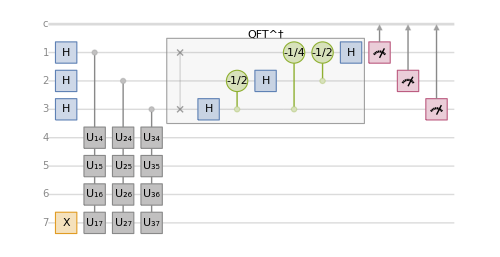

```mathematica
qc1=QuantumCircuitOperator["PhaseEstimation"[𝒰,3]][[4;;]];
qc1["Diagram",ImageSize->500]
```

Compute the measurement distribution:

```mathematica
measurement1=N[qc1][]
```

QuantumMeasurement[…]

Plot the distribution:

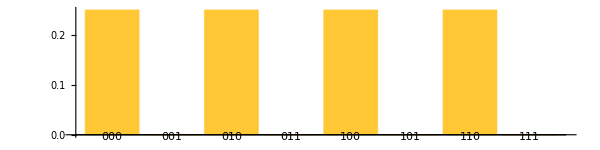

```mathematica
measurement1["ProbabilitiesPlot",AspectRatio->1/4]
```

Notice how there is a precisely equal chance to obtain one of four distinct eigenvalues from this phase estimation circuit. It turns out that sampling from these eigenvalues are in exact correspondence to sampling from a discrete uniform distribution k∈{0,…,r-1}, where r is the multiplicative order of 𝒶 modulo 𝒩.

To be more precise, the circuit output uniformly samples θ=x/2^s, where x∈{0,…,2^s-1}. While far from obvious, it can be shown that this is the same distribution as ϕ=k/r, where k∈{0,…,r-1}. This fact is key to the classical post-processing used to solve the order-finding problem.

### Post-Processing the Eigenvalue Estimations

For now, take for granted the curious fact about the distribution of sampled eigenvalues and the distribution for ϕ=k/r, where k∈{0,…,r-1}. You can use this fact to obtain r. Consider all possible outcomes that can be obtained by the previous circuit:

```mathematica
Keys@measurement1["Probability"]
```

{000,010,100,110}

Next, convert these to fractions which uniformly estimate ϕ=k/r:

```mathematica
ϕs=Map[FromDigits[First@#,2]/2^Length[First@#]&,Keys@measurement1["Probability"]]
```

{0,1/4,1/2,3/4}

Finally, the least common multiple of the denominators can be used to tell you r:

```mathematica
LCM@@Denominator[ϕs]
```

4

However, in any experiment you do not have direct access to the distribution of outcomes. Instead, you only have access to some specific outcomes from the distribution. Can you still use this to guess r?

Generate some simulated outcomes of running the circuit:

```mathematica
SeedRandom[12];
outcomes1=measurement1["SimulatedMeasurement",64]
```

{000,000,100,010,000,000,100,010,110,110,100,010,100,000,100,000,010,000,110,000,100,100,000,010,110,000,010,000,010,110,010,110,010,110,100,010,100,110,100,010,100,010,010,010,100,010,110,100,100,010,010,100,100,010,010,000,010,000,110,100,000,110,000,010}

As you can see from the plot below, this is far more runs of the circuit than needed to converge on the correct estimate for the multiplicative order of 𝒶 modulo 𝒩:

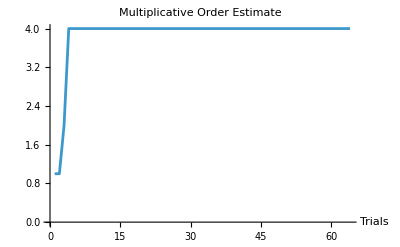

```mathematica
Module[{estimates},
estimates=Rest@FoldList[
LCM[#1,With[{list=#2["Name"]},Denominator[FromDigits[list,2]/(2^Length[list])]]]&,
1,outcomes1
];
ListLinePlot[estimates,PlotLabel->"Multiplicative Order Estimate",AxesLabel->{"Trials", None}]
]
```

For this particular 𝒶 and 𝒩, the chance to incorrectly estimate r decreases exponentially with the number of trials:

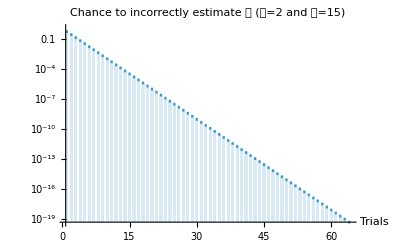

```mathematica
DiscretePlot[Power[2,-n],{n,64},ScalingFunctions->"Log",ExtentSize->1/2,GridLines->Automatic,PlotLabel->"Chance to incorrectly estimate 𝓇\n(𝒶=2 and 𝒩=15)",AxesLabel->{"Trials", None}]
```

The specifics of this post-processing may seem a bit mysterious, because they rely on some nontrivial intermediate theorems. You can still test this technique for other choices of 𝒩 and 𝒶 and note that it seems to work. The next section explores why this classical post-processing arrives at r.

### Exploring the Details

In the phase estimation circuit, you may have noticed that the ancilla qubits are prepared in the state 1. Why was this state chosen? Recall that the unitary operator used for M_𝒶 had four distinct eigenvalues because the multiplicative order of 2 modulo 15 was also equal to four.

What happens if you express the state 1 in a new basis? If you recall from linear algebra, a unitary matrix can be converted into a diagonal form using its eigenvectors as basis elements. If you don’t remember how to carry out this computation, the Quantum Framework can automate much of the process.

First, let’s label the new basis elements according to their eigenvalues (and an arbitrary index, since there are repeated eigenvalues):

```mathematica
𝒰eigenbasis=QuantumBasis@Association@With[{sys=𝒰["Eigensystem"]},
MapThread[QuditName[Subscript["ψ", "λ="<>ToString@TraditionalForm@#2]^(ToString@#1)]->#3&,{Range[Length@sys[[1]]],sys[[1]],sys[[2]]}]
]
```

QuantumBasis[…]

Now, each new basis vector has an arbitrary index and you can see its corresponding eigenvalue:

```mathematica
𝒰eigenbasis["ElementNames"]
```

{ψ_(λ=-1)^1,ψ_(λ=-1)^2,ψ_(λ=-1)^3,ψ_(λ=-1)^4,ψ_(λ=ⅈ)^5,ψ_(λ=ⅈ)^6,ψ_(λ=ⅈ)^7,ψ_(λ=-ⅈ)^8,ψ_(λ=-ⅈ)^9,ψ_(λ=-ⅈ)^10,ψ_(λ=1)^11,ψ_(λ=1)^12,ψ_(λ=1)^13,ψ_(λ=1)^14,ψ_(λ=1)^15,ψ_(λ=1)^16}

The state 1 has a nice feature when represented in this new basis. As you can see, it is a linear combination of one vector with each distinct eigenvalue:

```mathematica
QuantumState[QuantumState["0001"],𝒰eigenbasis]//TraditionalForm
```

-1/2ψ_(λ=-1)^4+ⅈ/2 ψ_(λ=ⅈ)^7-ⅈ/2ψ_(λ=-ⅈ)^10+1/2 ψ_(λ=1)^15

This (perhaps surprising) fact is what allows the quantum phase estimation algorithm to sample uniformly from the distinct eigenvalues.

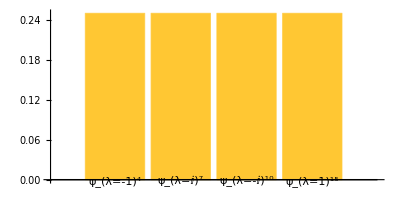

```mathematica
QuantumState[QuantumState["0001"],𝒰eigenbasis]["ProbabilityPlot",AspectRatio->1/2]
```

As long as enough register qubits are used to capture each possible eigenvalue, this idealized circuit will very quickly allow you to estimate r.

### Effects of Noise

In the previous analysis, the circuit was idealized with no noise channels. The circuit below adds a very simplistic noise model with a depolarizing channel immediately before measurement:

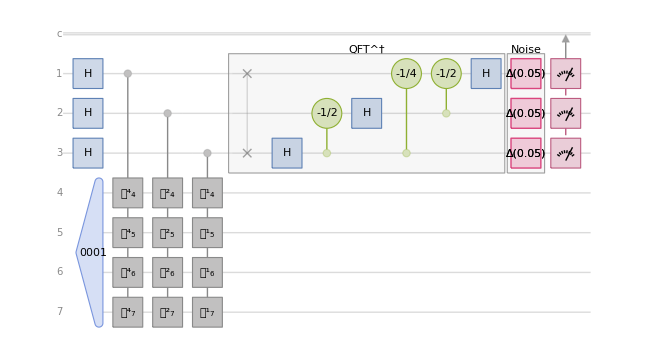

```mathematica
qc2=QuantumCircuitOperator[];
qc2["Diagram",ImageSize->650]
```

Compute the measurement probabilities:

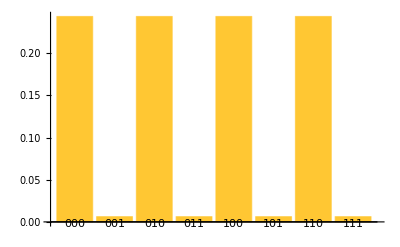

```mathematica
measurement2=N[qc2][];
measurement2["ProbabilityPlot"]
```

In the presence of noise, every outcome is now possible as an estimate for the eigenvalue, but the incorrect values are still less likely with this small amount of noise.

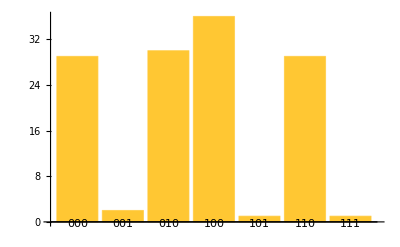

```mathematica
SeedRandom[12];
outcomes2=measurement2["SimulatedMeasurement",128];
BarChart[outcomes2//Counts//KeySort,ChartLabels->Automatic]
```

As you can see from the simulated results, the erroneous results happen with much lower frequency than the correct results. One naive post-processing strategy is to simply discard the results which occur less often than some acceptance threshold:

```mathematica
accepted2=Select[Counts@outcomes2,#>2&]
```

<|000→29,100→36,010→30,110→29|>

Now, proceed with the same post-processing as before:

```mathematica
noisyϕs=Map[FromDigits[First@#,2]/2^Length[First@#]&,Keys@accepted2]
```

{0,1/2,1/4,3/4}

```mathematica
LCM@@Denominator[noisyϕs]
```

4

This is the correct result for the multiplicative order of 2 modulo 15:

```mathematica
MultiplicativeOrder[2,15]
```

4

The remaining step in the algorithm is to see if 𝒶^(𝓇/2)-1mod 𝒩 is a nontrivial factor of 𝒩:

```mathematica
GCD[𝓃,Mod[𝒶^(4/2)-1,𝓃]]
```

3

This tells us that 3 is a factor of 15, as we expect.

Let’s explore this noisy distribution further:

```mathematica
noisy𝒟=measurement2["MultivariateDistribution"]
```

CategoricalDistribution[…]

You can compute the probability that any particular outcome will be an error from this specific noisy circuit:

```mathematica
Module[{errors,nonerrors},
nonerrors=First/@Keys@measurement1["Probability"];
errors=Complement[First/@Keys@measurement2["Probability"],nonerrors];
Probability[Or@@Thread[result==errors],result\[Distributed]noisy𝒟]
]
```

0.025

Next, you can compute the probability that less than 10% of the results will be erroneous:

```mathematica
Probability[x<n/10,x\[Distributed]BinomialDistribution[n,.025]]
```

Piecewise[{{BetaRegularized[0.975,1+n-Ceiling[n/10],Ceiling[n/10]], Ceiling[n/10]≥1}, {0, True}}]

For 128 trials, the chance of less than 10% of the outcomes being erroneous is greater than 0.999%:

```mathematica
%/.n->128
```

0.999978

You can see that increasing the number of trials leads to (generally) higher probability that 90% or more of the data is good:

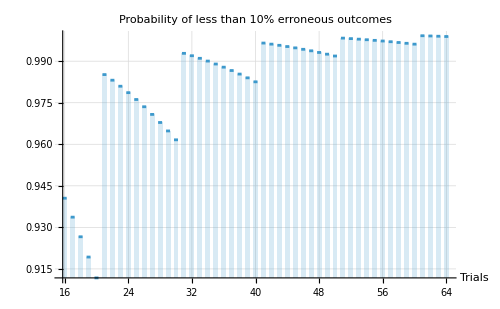

```mathematica
DiscretePlot[Evaluate@Probability[x<n/10,x\[Distributed]BinomialDistribution[n,.025]],{n,16,64},]
```

Using the trend in this plot allows you to discard the results that are clearly outliers due to noise.

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]